```mathematica
Notebook for the polynomial method in the Schroedinger equation. 
This example is for the case of the hexagonal well of side 1
```

Defining initialization variables

```mathematica
size=20;
L=1;
```

Symbolic integral of the generic x^n y^m integral term

```mathematica
$Assumptions={m≥0&&m∈Integers,n≥0&&n∈Integers,x∈Reals,y∈Reals};
integral[n_,m_]=1/((1+n) (2+m+n))2^(-2-m-n)* 3^((1+m)/2) (1+(-1)^m) (1+(-1)^n) (1+2^(2+m+n) (1+n) Beta[1/2,1+m,1+n]);
AbsoluteTiming[intTablehex=ParallelTable[integral[i,j],{i,0,200},{j,0,200},Method->"CoarsestGrained",DistributedContexts->Automatic];]
MyIntegral[n_,m_]:=MyIntegral[n,m]=intTablehex[[n+1,m+1]]
SetAttributes[MyIntegral,Listable]
AbsoluteTiming[ParallelTable[MyIntegral[i,j],{i,0,200},{j,0,200}];]
```

{3.30909,Null}

{1.56572,Null}

Creating data folder

```mathematica
shape="hexagon";
folder="~/agr_tese/data/symbolic_new/schrodinger/"<>shape<>"_";
basissize=ToString[Floor[size]];
CreateDirectory[folder<>basissize]//Quiet;
reg=Polygon[CirclePoints[L,6]];
```

Defining normalization, scalar product, and Hamiltonian integration elements

```mathematica
coeffs[func_]:=coeffs[func]=GroebnerBasis`DistributedTermsList[func,{x,y},MonomialOrder->DegreeLexicographic][[1,All]]
MyNorm[func1_]:=√MyProd[func1,func1]

MyProd[func1_,func2_]:=Collect[(coeffs[func1[x,y]*func2[x,y]][[All,2]]).MyIntegral[coeffs[func1[x,y]*func2[x,y]][[All,1,1]],coeffs[func1[x,y]*func2[x,y]][[All,1,2]]],{x,y},Simplify]

Ham[f1_,f2_]:=(f1[x,y])*(D[f2[x,y],{x,2}]+D[f2[x,y],{y,2}])
En[func1_]:=Simplify[-1*(func1[[All,2]]).MyIntegral[func1[[All,1,1]],func1[[All,1,2]]]]
```

Finding the numerical eigenvalues for comparison

```mathematica
exact=(4Tan[π/6])/6*NDEigenvalues[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈reg,size];
```

```mathematica
(*AbsoluteTiming[Table[CoefficientRules[ϕn[5,x,y]*ϕn[7,x,y]],{i,1,100}];]
AbsoluteTiming[Table[CoefficientRules[Simplify[ϕn[5,x,y]*ϕn[7,x,y]]],{i,1,100}];]
AbsoluteTiming[Table[CoefficientRules[Expand[ϕn[5,x,y]*ϕn[7,x,y]]],{i,1,100}];]*)
```

Defining the initial function

```mathematica
ϕu[1,x_,y_]=(y-(√3)/2 L)*(y+(√3)/2 L)*(x-(√3)/3 y-L)*(x-(√3)/3 y+L)*(x+(√3)/3 y-L)*(x+(√3)/3 y+L);
ϕn[1,x_,y_]=Simplify[(1/(MyNorm[ϕu[1,#1,#2]&]))*ϕu[1,x,y]];
D[ϕn[1,x,y],{x,2}]+D[ϕn[1,x,y],{y,2}]//AbsoluteTiming;
Ham[ϕn[1,#1,#2]&,ϕn[1,#1,#2]&]//AbsoluteTiming;
En[coeffs[Ham[ϕn[1,#1,#2]&,ϕn[1,#1,#2]&]]]//AbsoluteTiming
```

{0.007526,344974/47505}

```mathematica
AbsoluteTiming[CoefficientRules[ϕn[1,x,y],{x,y}];]
AbsoluteTiming[AAA=GroebnerBasis`DistributedTermsList[ϕn[1,x,y],{x,y},MonomialOrder->DegreeLexicographic][[1,All]];]
```

{0.006486,Null}

{0.001252,Null}

```mathematica
f[m_,x_,y_]:=If[Mod[(m-1)-(Floor[√(m-1)])^2,2]==0,x^Floor[√(m-1)]*y^(((m-1)-(Floor[√(m-1)])^2)/2),x^(((m-1)-(Floor[√(m-1)])^2-1)/2)*y^Floor[√(m-1)]]
For[counter=2,counter<size+1,counter++,
ϕu[counter,x_,y_]=f[counter,x,y]*ϕn[1,x,y]-ParallelSum[MyProd[f[counter,x,y]*ϕn[1,#1,#2]&,ϕn[n,#1,#2]&]*ϕn[n,x,y],{n,1,counter-1},Method->"FinestGrained"];
ϕn[counter,x_,y_]=Simplify[ϕu[counter,x,y]/MyNorm[ϕu[counter,#1,#2]&]];
Print[counter]]//AbsoluteTiming
Basis[x_,y_]=Table[ϕn[i,x,y],{i,1,size}];
Length[Basis[x,y]]
```

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

{33.9895,Null}

20

Uncomment this table for verification of the orthogonality of the basis

```mathematica
(*ortho=ParallelTable[MyProd[Basis[#1,#2][[b]]&,Basis[#1,#2][[c]]&],{b,1,size},{c,1,i},Method->"FinestGrained",DistributedContexts->Automatic];//AbsoluteTiming
orthofull=MapThread[Join,{ortho,Rest/@Flatten[Conjugate[ortho],{{2},{1}}]}];]
MatrixForm[orthofull]//Chop*)
```

Calculate the Hamiltonian matrix
It is Hermitian, so only the upper-triangular matrix is calculated

```mathematica
AbsoluteTiming[H=ParallelTable[Ham[ϕn[i,#1,#2]&,ϕn[j,#1,#2]&],{i,1,size},{j,1,i},Method->"FinestGrained",DistributedContexts->Automatic];]
```

{0.665702,Null}

```mathematica
AbsoluteTiming[Hn=ParallelTable[coeffs[N[H[[i,j]],100]],{i,1,size},{j,1,i},Method->"FinestGrained",DistributedContexts->Automatic];]
```

{3.80504,Null}

```mathematica
AbsoluteTiming[H2=ParallelTable[En[Hn[[i,j]]],{i,1,size},{j,1,i},Method->"FinestGrained",DistributedContexts->Automatic];]
AbsoluteTiming[Hfull=MapThread[Join,{H2,Rest/@Flatten[Conjugate[H2],{{2},{1}}]}];]
MatrixForm[Hfull]
```

{0.817451,Null}

{0.000224,Null}

(7.2618461214609 | 0 | 0 | 0 | -1.08305116282 | -1.19637544233 | 0 | 0 | -0.627748395765 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.09148857124 | -1.07201472552 | 0 | 0
0 | 18.19131024551 | 0 | 0 | 0 | 0 | 0 | 0.27531141802 | 0 | 0.58856702975 | 0 | 0 | 0 | 0.80638637175 | 0 | 0 | 0 | 0 | 0 | -1.0355820453
0 | 0 | 18.19131024551 | 0 | 0 | 0 | 0.2872438496 | 0 | 0 | 0 | 0.58283659483 | 0 | 0 | 0 | -1.6169320452 | 0 | 0 | 0 | 0.06064526225 | 0
0 | 0 | 0 | 33.03588823536 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.30609933916 | 2.6173397807 | 0 | 0 | 0.2265354175 | 0 | 0 | 0 | 0
-1.08305116282 | 0 | 0 | 0 | 35.5759384049 | 2.80582649226 | 0 | 0 | 3.8328273057 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.079198777 | 0.3657600282 | 0 | 0
-1.19637544233 | 0 | 0 | 0 | 2.80582649226 | 36.1353003647 | 0 | 0 | 0.8827206936 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.064472994 | 7.1016958098 | 0 | 0
0 | 0 | 0.2872438496 | 0 | 0 | 0 | 57.6450391473 | 0 | 0 | 0 | 3.8540957622 | 0 | 0 | 0 | 5.1929429482 | 0 | 0 | 0 | 17.780828634 | 0
0 | 0.27531141802 | 0 | 0 | 0 | 0 | 0 | 51.5378687296 | 0 | 6.5147509954 | 0 | 0 | 0 | 7.3414379482 | 0 | 0 | 0 | 0 | 0 | 7.8465708114
-0.627748395765 | 0 | 0 | 0 | 3.8328273057 | 0.8827206936 | 0 | 0 | 79.7012313756 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.913051349 | 3.334358202 | 0 | 0
0 | 0.58856702975 | 0 | 0 | 0 | 0 | 0 | 6.5147509954 | 0 | 62.4178755206 | 0 | 0 | 0 | 10.144966898 | 0 | 0 | 0 | 0 | 0 | 2.618063204
0 | 0 | 0.58283659483 | 0 | 0 | 0 | 3.8540957622 | 0 | 0 | 0 | 63.5658083106 | 0 | 0 | 0 | 0.147602743 | 0 | 0 | 0 | 3.947725632 | 0
0 | 0 | 0 | 5.30609933916 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 91.438716618 | 13.191882726 | 0 | 0 | 10.75078168 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2.6173397807 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.191882726 | 83.436294167 | 0 | 0 | 10.28395832 | 0 | 0 | 0 | 0
0 | 0.80638637175 | 0 | 0 | 0 | 0 | 0 | 7.3414379482 | 0 | 10.144966898 | 0 | 0 | 0 | 118.66304454 | 0 | 0 | 0 | 0 | 0 | 14.67352311
0 | 0 | -1.6169320452 | 0 | 0 | 0 | 5.1929429482 | 0 | 0 | 0 | 0.147602743 | 0 | 0 | 0 | 107.04413173 | 0 | 0 | 0 | 16.1231986 | 0
0 | 0 | 0 | 0.2265354175 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.75078168 | 10.28395832 | 0 | 0 | 149.4602623 | 0 | 0 | 0 | 0
-1.09148857124 | 0 | 0 | 0 | 6.079198777 | 2.064472994 | 0 | 0 | 11.913051349 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 98.211059487 | 1.065399114 | 0 | 0
-1.07201472552 | 0 | 0 | 0 | 0.3657600282 | 7.1016958098 | 0 | 0 | 3.334358202 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.065399114 | 103.07172964 | 0 | 0
0 | 0 | 0.06064526225 | 0 | 0 | 0 | 17.780828634 | 0 | 0 | 0 | 3.947725632 | 0 | 0 | 0 | 16.1231986 | 0 | 0 | 0 | 150.19629573 | 0
0 | -1.0355820453 | 0 | 0 | 0 | 0 | 0 | 7.8465708114 | 0 | 2.618063204 | 0 | 0 | 0 | 14.67352311 | 0 | 0 | 0 | 0 | 0 | 122.39096285)

Obtaining the numerical eigenvalues and eigenvectors

```mathematica
eval=Eigenvalues[Hfull];//AbsoluteTiming
evec=Eigenvectors[Hfull];
```

{0.011863,Null}

Plotting the eigenvalues

{2.90339561,7.35644285,7.3615764,13.1746547,13.178025,15.2729674,19.4371946,21.6022527,25.4102489,26.0546605,29.8388367,29.8609483,39.5374432,41.2241402,41.24106,43.1656679,43.4456434,55.8780055,62.2861417,64.4987687}

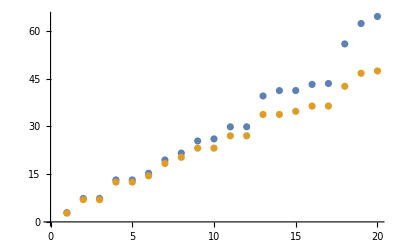

```mathematica
Sort[Abs[eval]/(π^2/4)]
ListPlot[{Sort[Abs[eval]/(π^2/4)],exact}]
```

Defining the eigenbasis

```mathematica
For[i=1,i<size+1,i++,
mode[i,x_,y_]=(evec[[i]]).Basis[x,y];
Print[i]]//AbsoluteTiming
BasisN[x_,y_]=Table[mode[aa,x,y],{aa,1,size}];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

{0.027801,Null}

Comparing eigenvalues

```mathematica
AAAA=Sort[Table[(Conjugate[evec].Hfull.Transpose[evec])[[i,i]],{i,1,size}]];
```

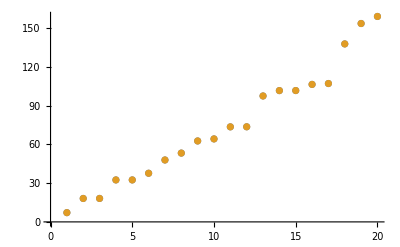

```mathematica
ListPlot[{AAAA,Sort[Re[Abs[eval]]]}]
```

Exporting the data

```mathematica
Export[folder<>basissize<>"/eigenvalues.dat",Append[Sort[Re[Abs[eval]]],]]
Export[folder<>basissize<>"/basis.m",Basis[x,y]]
Export[folder<>basissize<>"/eigenvectors.m",evec]
Export[folder<>basissize<>"/full_hamiltonian.m",Hfull]
Export[folder<>basissize<>"/eigenfunctions.m",Table[mode[aa,x,y],{aa,1,size}]]
```

~/agr_tese/data/symbolic_new/schrodinger/hexagon_20/eigenvalues.dat

~/agr_tese/data/symbolic_new/schrodinger/hexagon_20/basis.m

~/agr_tese/data/symbolic_new/schrodinger/hexagon_20/eigenvectors.m

~/agr_tese/data/symbolic_new/schrodinger/hexagon_20/full_hamiltonian.m

~/agr_tese/data/symbolic_new/schrodinger/hexagon_20/eigenfunctions.m

Plotting the eigenfunctions

```mathematica
(*ParallelTable[{Plot3D[BasisN[x,y][[aa]],{x,y}∈reg,ImageSize->Large],DensityPlot[Abs[BasisN[x,y][[aa]]]^2,{x,y}∈reg,ImageSize->Large,ColorFunction->"SunsetColors",PlotPoints->100]},{aa,size,1,-1},Method->"CoarsestGrained",DistributedContexts->Automatic]//AbsoluteTiming*)
```